## Figure S2A

```mathematica
(*proportion of alpha sequences*)alphaFullFreq=0.01{0.536,0.536,0.554,0.964,1.435,1.485,1.362,1.97,2.197,2.087,2.721,2.956,3.107,3.519,4.096,5.289,5.946,6.205,6.488,7.295,7.604,8.116,6.902,8.11,10.15,9.823,9.564,10.354,10.714,12.239,12.576};
(*proportion of alpha sequences used for the exp fit*)
alphaFreq=0.01{0.964,1.435,1.485,1.362,1.97,2.197,2.087,2.721,2.956,3.107,3.519,4.096,5.289,5.946,6.205,6.488,7.295,7.604,8.116,6.902,8.11,10.15,9.823,9.564,10.354,10.714,12.239,12.576};
alphaTime=Table[i,{i,1,Length[alphaFreq]}];
data=MapThread[List,{alphaTime,alphaFreq}];
(*expression for the line of best fit*)
model=NonlinearModelFit[data, a Exp[s x],{a,s},x,MaxIterations->Infinity]
(*confidence interval for the selective advantage parameter, in units of 1 generation*)
model["ParameterConfidenceIntervals"][[2]]*5.2
```

FittedModel[0.0181533 ⅇ^(0.0711946 x)]

{0.329381,0.411043}

{0.0181533 ⅇ^(0.0711946 x),0.0181533 ⅇ^(0.0711946 x)-2.05553 √(ⅇ^(0.142389 x) (2.49052×10^-6-2.1154×10^-7 x+4.80891×10^-9 x^2)),0.0181533 ⅇ^(0.0711946 x)+2.05553 √(ⅇ^(0.142389 x) (2.49052×10^-6-2.1154×10^-7 x+4.80891×10^-9 x^2))}

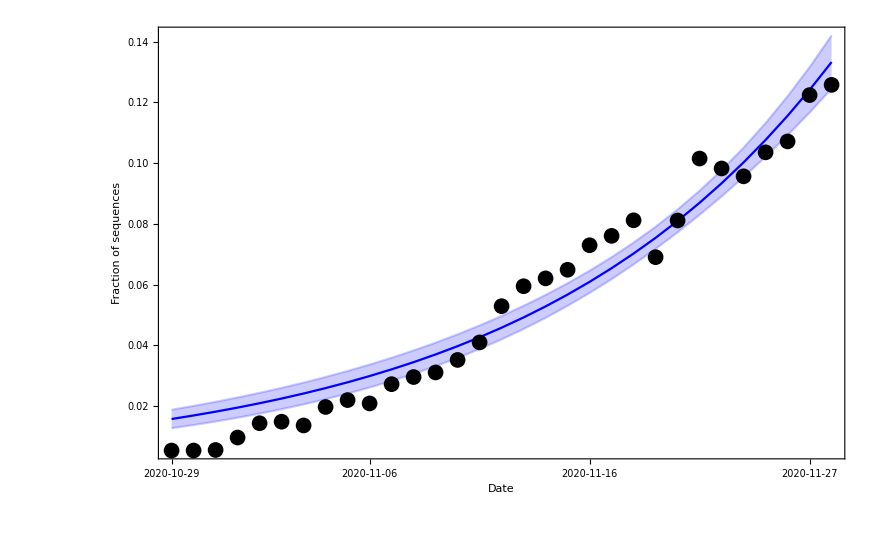

```mathematica
plot=ListPlot[alphaFullFreq,PlotStyle->Black];
delay=Length[alphaFullFreq]-Length[alphaFreq];
(*plotting proportion of sequences, line of best fit, and mean prediction bands*)
Join[{model["BestFit"]},model["MeanPredictionBands"]]
Show[ListPlot[{Table[{x,0.0181533248664466 ⅇ^(0.07119460585518311 (x-delay))},{x,1,delay+28}],Table[{x,0.0181533248664466 ⅇ^(0.07119460585518311 (x-delay))-2.055529438642873 √(ⅇ^(0.14238921171036623 (x-delay)) (2.490515332384898*^-6-2.1153981112259068*^-7 (x-delay)+4.808912035628019*^-9 (x-delay)^2))},{x,1,delay+28}],Table[{x,0.0181533248664466 ⅇ^(0.07119460585518311 (x-delay))+2.055529438642873 √(ⅇ^(0.14238921171036623 (x-delay)) (2.490515332384898*^-6-2.1153981112259068*^-7 (x-delay)+4.808912035628019*^-9 (x-delay)^2))},{x,1,delay+28}]},PlotStyle->{{Blue},{Blue,Opacity[0.2]},{Blue,Opacity[0.2]}},Joined->True,Filling->{2->{3}},FillingStyle->{Blue,Opacity[0.2]},Frame->True,FrameTicks->{{Automatic,Automatic},{{{1,"2020-10-29"},{10,"2020-11-06"},{20,"2020-11-16"},{30,"2020-11-27"},{40,"2020-12-13"}},Automatic}},PlotRange->All,FrameLabel->{"Date","Fraction of sequences"},FrameStyle->{{Directive[Black,22],Directive[Black,22]},{Directive[Black,22],Directive[Black,18]}},ImageSize->900],plot,PlotRange->All,ImageSize->880]
```

## Figure S2B

```mathematica
(*proportion of beta sequences*)betaFullFreq=0.01{0,0.826,2.479,2.521,3,3.225,2.8301,2.654,0.9,0.001,1.19,1.098,1.162,3.22,2.479,2.985,4.026,4.568,4.265,4.166,3.61,5.179,6.083,6.802,8.518,9.23,8.45,9.848,12.359,15.175,18.385,23.943};
(*proportion of beta sequences used for the exp fit*)
betaFreq=0.01{1.19,1.098,1.162,3.22,2.479,2.985,4.026,4.568,4.265,4.166,3.61,5.179,6.083,6.802,8.518,9.23,8.45,9.848,12.359,15.175,18.385,23.943};
betaTime=Table[i,{i,1,Length[betaFreq]}];
data=MapThread[List,{betaTime,betaFreq}];
(*expression for the line of best fit*)
model=NonlinearModelFit[data, a Exp[s x],{a,s},x,MaxIterations->Infinity]
(*confidence interval for the selective advantage parameter, in units of 1 generation*)
model["ParameterConfidenceIntervals"][[2]]*5.2
```

FittedModel[0.00918955 ⅇ^(0.142786 x)]

{0.650131,0.834845}

{0.00918955 ⅇ^(0.142786 x),0.00918955 ⅇ^(0.142786 x)-2.08596 √(ⅇ^(0.285572 x) (2.28277×10^-6-2.32836×10^-7 x+6.12221×10^-9 x^2)),0.00918955 ⅇ^(0.142786 x)+2.08596 √(ⅇ^(0.285572 x) (2.28277×10^-6-2.32836×10^-7 x+6.12221×10^-9 x^2))}

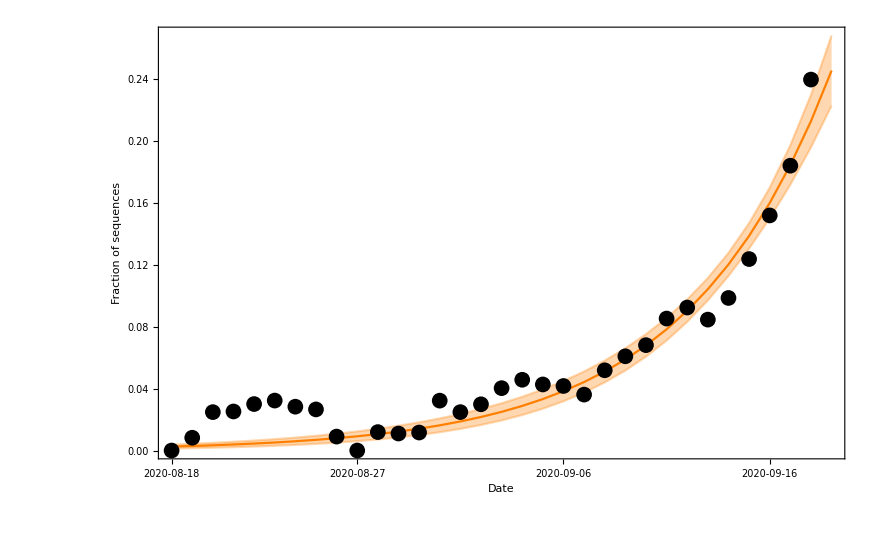

```mathematica
(*plotting proportion of sequences, line of best fit, and mean prediction bands*)
plot=ListPlot[betaFullFreq,PlotStyle->Black];
delay=Length[betaFullFreq]-Length[betaFreq];
Join[{model["BestFit"]},model["MeanPredictionBands"]]
Show[ListPlot[{Table[{x,0.009189551746308283 ⅇ^(0.14278619242624735 (x-delay))},{x,1,delay+23}],Table[{x,0.009189551746308283 ⅇ^(0.14278619242624735 (x-delay))-2.085963447265865 √(ⅇ^(0.2855723848524947 (x-delay)) (2.282774246974715*^-6-2.3283607952566307*^-7 (x-delay)+6.1222126547195345*^-9 (x-delay)^2))},{x,1,delay+23}],Table[{x,0.009189551746308283 ⅇ^(0.14278619242624735 (x-delay))+2.085963447265865 √(ⅇ^(0.2855723848524947 (x-delay)) (2.282774246974715*^-6-2.3283607952566307*^-7 (x-delay)+6.1222126547195345*^-9 (x-delay)^2))},{x,1,delay+23}]},PlotStyle->{{Orange},{Orange,Opacity[0.3]},{Orange,Opacity[0.3]}},Joined->True,Filling->{2->{3}},FillingStyle->{Orange,Opacity[0.3]},Frame->True,FrameTicks->{{Automatic,Automatic},{{{1,"2020-08-18"},{10,"2020-08-27"},{20,"2020-09-06"},{30,"2020-09-16"},{40,"2020-12-13"}},Automatic}},PlotRange->All,FrameLabel->{"Date","Fraction of sequences"},FrameStyle->{{Directive[Black,22],Directive[Black,22]},{Directive[Black,22],Directive[Black,18]}},ImageSize->900],plot,PlotRange->All,ImageSize->880]
```

## Figure S2C

```mathematica
(*proportion of gamma sequences*)
gammaFullFreq=0.01{0,0.526,0.473,0.429,2.4096,
1.9733,2.114,2.034,1.851,1.662,1.526,0.225,0.691,0.228,0.233,0.22,0.75,0.813,0.99,1.013,2.173,2.135,2.621,3.296,3.26,2.99,2.422,1.265,1.307,1.01,0.001,0.001,3.289,6.752,10.03,10.942,10.882,18.387,20.623,24.708,24.681,26.605};
(*proportion of gamma sequences used for the exp fit*)
gammaFreq=0.01{3.289,6.752,10.03,10.942,10.882,18.387,20.623,24.708,24.681,26.605};
gammaTime=Table[i,{i,1,Length[gammaFreq]}];
data=MapThread[List,{gammaTime,gammaFreq}];
(*expression for the line of best fit*)
model=NonlinearModelFit[data, a Exp[s x],{a,s},x,MaxIterations->Infinity]
(*confidence interval for the selective advantage parameter, in units of 1 generation*)
model["ParameterConfidenceIntervals"][[2]]*5.2
```

FittedModel[0.0586825 ⅇ^(0.161548 x)]

{0.59067,1.08943}

{0.0586825 ⅇ^(0.161548 x),0.0586825 ⅇ^(0.161548 x)-2.306 √(ⅇ^(0.323096 x) (0.0000981351-0.0000232033 x+1.48939×10^-6 x^2)),0.0586825 ⅇ^(0.161548 x)+2.306 √(ⅇ^(0.323096 x) (0.0000981351-0.0000232033 x+1.48939×10^-6 x^2))}

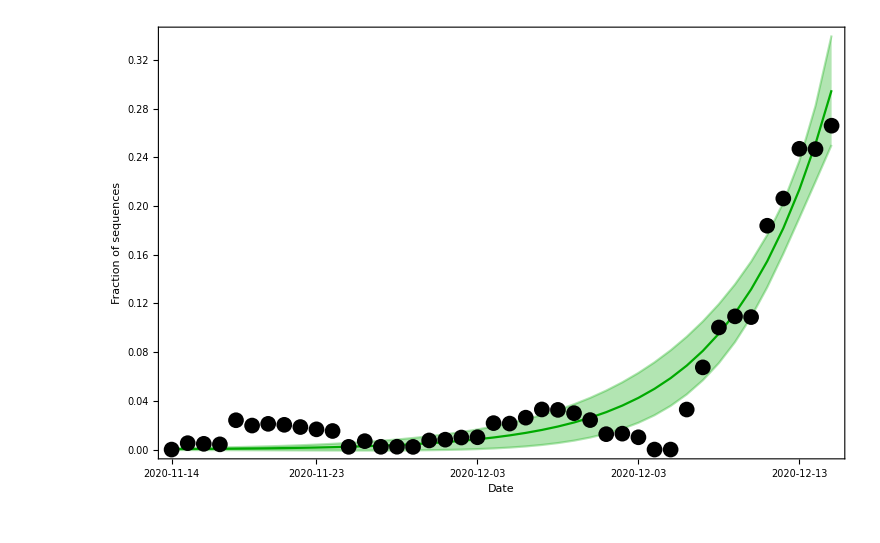

```mathematica
(*plotting proportion of sequences, line of best fit, and mean prediction bands*)
plot=ListPlot[gammaFullFreq,PlotStyle->Black];
delay=Length[gammaFullFreq]-Length[gammaFreq];
Join[{model["BestFit"]},model["MeanPredictionBands"]]
Show[ListPlot[{Table[{x,0.05868248470253203 ⅇ^(0.16154794705804945 (x-delay))},{x,1,delay+10}],Table[{x,0.05868248470253203 ⅇ^(0.161547944387456 (x-delay))-2.306004135204168 √(ⅇ^(0.323095888774912 (x-delay)) (0.000098135086928004-0.00002320333658282943 (x-delay)+1.4893941020054592*^-6 (x-delay)^2))},{x,1,delay+10}],Table[{x,0.05868248470253203 ⅇ^(0.161547944387456 (x-delay))+2.306004135204168 √(ⅇ^(0.323095888774912 (x-delay)) (0.000098135086928004-0.00002320333658282943 (x-delay)+1.4893941020054592*^-6 (x-delay)^2))},{x,1,delay+10}]},PlotStyle->{{Darker[Green]},{Darker[Green],Opacity[0.3]},{Darker[Green],Opacity[0.3]}},Joined->True,Filling->{2->{3}},FillingStyle->{Darker[Green],Opacity[0.3]},Frame->True,FrameTicks->{{Automatic,Automatic},{{{1,"2020-11-14"},{10,"2020-11-23"},{20,"2020-12-03"},{30,"2020-12-03"},{40,"2020-12-13"}},Automatic}},PlotRange->All,FrameLabel->{"Date","Fraction of sequences"},FrameStyle->{{Directive[Black,22],Directive[Black,22]},{Directive[Black,22],Directive[Black,18]}},ImageSize->900],plot,ImageSize->880]
```